# 结果测试

## 杨朝辉 PB17071433

```mathematica
Needs["ConstantPotential`"]
```

## 以电子为例，SI单位制下

## 求本征能量谱

```mathematica
(*电子及势函阱参数设置*)
a=1.0*10^-9;
q=1.602*10^-19;
V0=2q;
μ=9.01*10^-31;
energyOdd=EnergyOdd[V0,2a,μ]/q
energyEven=EnergyEven[V0,2a,μ]/q
energySpectrum=EnergySpectrum[V0,2a,μ]/q
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-1.71085,-0.872367}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-1.92737,-1.35531,-0.296593}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-1.92737,-1.71085,-1.35531,-0.872367,-0.296593}

## 绘制能级图

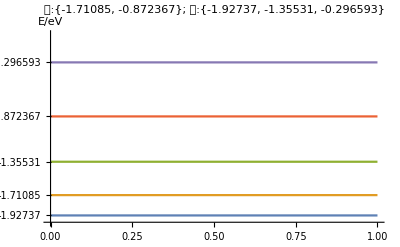

```mathematica
Plot[energySpectrum,{x,0,1},AxesOrigin->{0,Floor[energySpectrum[[1]]]},
AxesLabel->{None,"E/eV"},Ticks->{None,energySpectrum},
PlotLabel->Style[StringJoin["奇:",ToString[energyOdd],"; 偶:",ToString[energyEven]],FontSize->11,FontColor->Blue]]
```

## 求本征函数

#### 奇宇称

```mathematica
u1:=WaveOdd[x,V0,2a,μ,energyOdd[[1]]*q]
u2:=WaveOdd[x,V0,2a,μ,energyOdd[[2]]*q]
ToExpression[u1]
ToExpression[u2]
```

ToExpression::notstrbox: Piecewise[{{9.04842×10^6 ⅇ^(6.69308×10^9 x), x<-1.×10^-9}, {-29496. Sin[2.75155×10^9 x], Abs[x]≤1.×10^-9}, {-9.04842×10^6 ⅇ^(-6.69308×10^9 x), x>1.×10^-9}, {0, True}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed

ToExpression::notstrbox: Piecewise[{{2.57016×10^6 ⅇ^(4.77935×10^9 x), x<-1.×10^-9}, {28757.1 Sin[5.4338×10^9 x], Abs[x]≤1.×10^-9}, {-2.57016×10^6 ⅇ^(-4.77935×10^9 x), x>1.×10^-9}, {0, True}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed

#### 偶宇称

```mathematica
v1:=WaveEven[x,V0,2a,μ,energyEven[[1]]*q]
v2:=WaveEven[x,V0,2a,μ,energyEven[[2]]*q]
v3:=WaveEven[x,V0,2a,μ,energyEven[[3]]*q]
ToExpression[v1]
ToExpression[v2]
ToExpression[v3]
Length[Range[-1.5a,1.5a,a/30]]
```

ToExpression::notstrbox: Piecewise[{{6.86544×10^6 ⅇ^(7.10398×10^9 x), x<-1.×10^-9}, {29607.5 Cos[1.37906×10^9 x], Abs[x]≤1.×10^-9}, {6.86544×10^6 ⅇ^(-7.10398×10^9 x), x>1.×10^-9}, {0, True}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed

ToExpression::notstrbox: Piecewise[{{6.42128×10^6 ⅇ^(5.95715×10^9 x), x<-1.×10^-9}, {-29262. Cos[4.10861×10^9 x], Abs[x]≤1.×10^-9}, {6.42128×10^6 ⅇ^(-5.95715×10^9 x), x>1.×10^-9}, {0, True}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed

ToExpression::notstrbox: Piecewise[{{406290. ⅇ^(2.78676×10^9 x), x<-1.×10^-9}, {27127.9 Cos[6.67849×10^9 x], Abs[x]≤1.×10^-9}, {406290. ⅇ^(-2.78676×10^9 x), x>1.×10^-9}, {0, True}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed

91

## 绘制波函数（已归一化）图像

#### 奇宇称

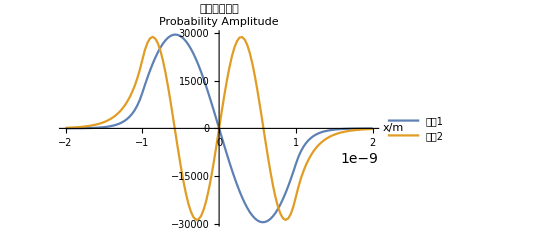

```mathematica
xs=Range[-2a,2a,a/30];
ys1=Table[u1/.x->xs[[i]],{i,1,Length[xs]}];
ys2=Table[u2/.x->xs[[i]],{i,1,Length[xs]}];
ListPlot[{Transpose[{xs,ys1}],Transpose[{xs,ys2}]},
	AxesLabel->{"x/m","Probability Amplitude"},
	Joined->True,PlotLegends->{"能级1","能级2"},PlotLabel->"奇宇称波函数"]
```

#### 偶宇称

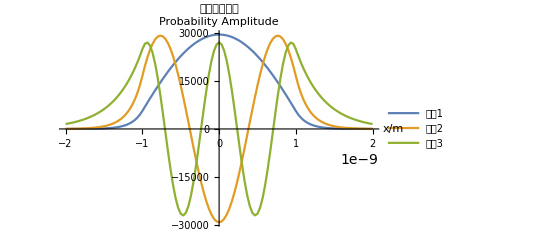

```mathematica
xs=Range[-2a,2a,a/30];
ys1=Table[v1/.x->xs[[i]],{i,1,Length[xs]}];
ys2=Table[v2/.x->xs[[i]],{i,1,Length[xs]}];
ys3=Table[v3/.x->xs[[i]],{i,1,Length[xs]}];
ListPlot[{Transpose[{xs,ys1}],Transpose[{xs,ys2}],Transpose[{xs,ys3}]},
	AxesLabel->{"x/m","Probability Amplitude"},
	Joined->True,PlotLegends->{"能级1","能级2","能级3"},PlotLabel->"偶宇称波函数"]
```